# Corner Flow general solution

```mathematica
vx = -B-D*ArcTan[x,z] + (C*x + D*z)(-x/(x^2+z^2))
vz = A+C*ArcTan[x,z] + (C*x + D*z)(-z/(x^2+z^2))
```

-B-(x (C x+D z))/(x^2+z^2)-D ArcTan[x,z]

A-(z (C x+D z))/(x^2+z^2)+C ArcTan[x,z]

## Apply boundary conditions for continental arc corner flow

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->0,z->0}]
eq2 = ReplaceAll[vz,{ArcTan[x,z]->0,z->0}]
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]
solarc =Solve[eq1==0&&eq2==0&&eq3==Cos[δ]&&eq4==-Sin[δ],{A,B,C,D},Reals,Assumptions->{δ>0,δ<Pi/2}]
```

-B-C

A

-B+D δ-(x (C x-D x Tan[δ]))/(x^2+x^2 Tan[δ]^2)

A-C δ+(x Tan[δ] (C x-D x Tan[δ]))/(x^2+x^2 Tan[δ]^2)

{{A→0,B→-(2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),C→(2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),D→(2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2)+(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2))/(2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ])}}

```mathematica
δval = 30*Pi/180;
solplot=ReplaceAll[solarc,{δ->δval}];
Aval=A/.solplot[[1]]
Bval=B/.solplot[[1]]//FullSimplify
Cval=C/.solplot[[1]]//FullSimplify
Dval=D/.solplot[[1]]//FullSimplify
```

0

-(3 π)/(-9+π^2)

(3 π)/(-9+π^2)

(9 (16/(√3)-(8 π)/(-9+π^2)))/(8 (3 √3+2 π))

# Plot velocity field

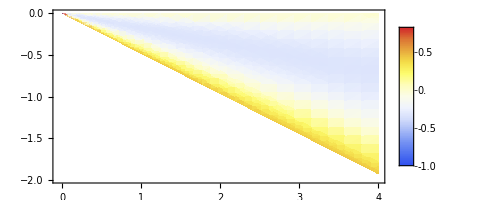

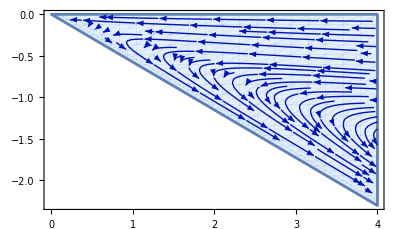

```mathematica
toplotx=ReplaceAll[vx,{A->Aval,B->Bval,C->Cval,D->Dval}];
toplotz=ReplaceAll[vz,{A->Aval,B->Bval,C->Cval,D->Dval}];
(*D[toplotx,z]+D[toplotz,x]//FullSimplify*)
DensityPlot[toplotx,{x,-0.04,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval],AspectRatio->Automatic]
(*RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval]*)
StreamPlot[{toplotx,toplotz},{x,-0.01,4},{z,-4*Tan[δval],0},RegionFunction->Function[{x,z},z+Tan[δval]*x>=0],StreamPoints->Fine,StreamScale->Large,AspectRatio->Automatic]
```